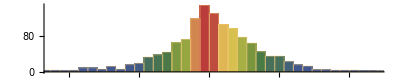

```mathematica
Histogram[
Differences@
FinancialData["NASDAQ:GOOG", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5]
```

```mathematica
Histogram[
Differences@
FinancialData["NASDAQ:GOOG", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

-Graphics-

```mathematica
Histogram[
Differences@
FinancialData["NASDAQ:GOOG", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5]
```

-Graphics-

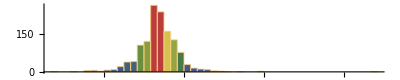

```mathematica
Histogram[
Ratios@
FinancialData["NASDAQ:GOOG", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

```mathematica
Histogram[
Differences@
FinancialData["NASDAQ:GOOG", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

-Graphics-

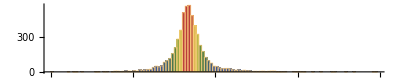

```mathematica
Histogram[
Ratios@
FinancialData["NASDAQ:AMZN", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

```mathematica
Histogram[
Differences@
FinancialData["NASDAQ:AMZN", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

-Graphics-

```mathematica
Histogram[
Differences@
FinancialData["NYSE:IBM", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

-Graphics-

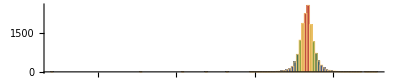

```mathematica
Histogram[
Ratios@
FinancialData["NYSE:IBM", "Price", All]["Values"],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

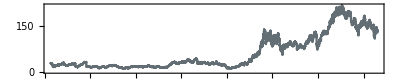

```mathematica
DateListPlot[
FinancialData["NYSE:IBM", "Price", All],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

```mathematica
DateListLogPlot[
FinancialData["NYSE:IBM", "Price", All],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

-Graphics-

```mathematica
With[{list=FinancialData["NYSE:IBM", "Price", All]},
Transpose[{
list["Dates"][[;;-2]],
Differences@list
}]]
```

Transpose::nmtx: The first two levels of {{DateObject[{1962,1,2,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,1,3,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,1,4,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,1,5,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,1,8,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,1,9,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,1,10,0,0,0.},Instant,Gregorian,-7.],«37»,DateObject[{1962,3,6,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,3,7,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,3,8,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,3,9,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,3,12,0,0,0.},Instant,Gregorian,-7.],DateObject[{1962,3,13,0,0,0.},Instant,Gregorian,-7.],«14420»},TemporalData[«1»]} cannot be transposed.

$Aborted[]

```mathematica
With[{list=FinancialData["NYSE:IBM", "Price", All]},
Transpose[{
list["Dates"][[;;-2]],
Differences@list["Values"]
}]]
```

{{Tue 2 Jan 1962 00:00:00GMT-7.,0.25 $},{Wed 3 Jan 1962 00:00:00GMT-7.,-0.29 $},{Thu 4 Jan 1962 00:00:00GMT-7.,-0.56 $},{Fri 5 Jan 1962 00:00:00GMT-7.,-0.52 $},{Mon 8 Jan 1962 00:00:00GMT-7.,0.32 $},{Tue 9 Jan 1962 00:00:00GMT-7.,0.05 $},{Wed 10 Jan 1962 00:00:00GMT-7.,0.30 $},{Thu 11 Jan 1962 00:00:00GMT-7.,0.05 $},{Fri 12 Jan 1962 00:00:00GMT-7.,0.13 $},{Mon 15 Jan 1962 00:00:00GMT-7.,-0.30 $},14451,{Mon 3 Jun 2019 00:00:00GMT-7.,4.42 $},{Tue 4 Jun 2019 00:00:00GMT-7.,-1.20 $},{Wed 5 Jun 2019 00:00:00GMT-7.,0.73 $},{Thu 6 Jun 2019 00:00:00GMT-7.,1.09 $},{Fri 7 Jun 2019 00:00:00GMT-7.,1.43 $},{Mon 10 Jun 2019 00:00:00GMT-7.,1.21 $},{Tue 11 Jun 2019 00:00:00GMT-7.,-1.08 $},{Wed 12 Jun 2019 00:00:00GMT-7.,0.89 $},{Thu 13 Jun 2019 00:00:00GMT-7.,-0.61 $}}
 |  |  |  |

```mathematica
DateListPlot[
Transpose[{
list["Dates"][[;;-2]],
Differences@list["Values"]
}],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]
```

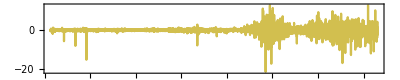

```mathematica
With[{list=FinancialData["NYSE:IBM", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]],
Differences@list["Values"]
}],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]]
```

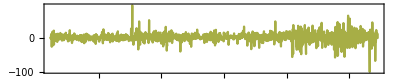

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]],
Differences@list["Values"]
}],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]]
```

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
DateListLogPlot[
Transpose[{
list["Dates"][[;;-2]],
Differences@list["Values"]
}],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]]
```

-Graphics-

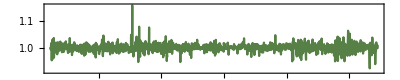

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]],
Ratios@list["Values"]
}],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]]
```

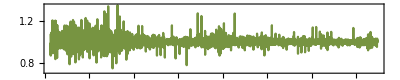

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]],
Ratios@list["Values"]
}],
ImageSize->Full, ColorFunction->"DarkRainbow", AspectRatio->1/5,PlotRange->Full]]
```

```mathematica
With[{text=ExampleData[{"Text","DonQuixoteIEnglish"}]},
FindClusters@
ToLowerCase@
Select[Characters@text,LetterQ]
]
```

$Aborted

```mathematica
FindDistribution@
Differences@
FinancialData["NYSE:IBM", "Price", All]["Values"]
```

```mathematica
FindDistribution@
Differences@
FinancialData["NASDAQ:FB", "Price", All]["Values"]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

FindDistribution::nodata: The number of data points has to be greater than 1.

FindDistribution[Differences[$Failed[Values]]]

```mathematica
FindDistribution@
Differences@
FinancialData["NASDAQ:FB", "Price", All]["Values"]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

FindDistribution::nodata: The number of data points has to be greater than 1.

FindDistribution[Differences[$Failed[Values]]]

```mathematica
FindDistribution@
Differences@
FinancialData["NASDAQ:FB", "Price", All]["Values"]
```

FindDistribution::wrgfmt: Argument … at position 1 does not have the right format. Data should be a numerical array of depth less than 2.

FindDistribution[{-4.20 $,-3.03 $,1.00 $,1.03 $,-1.12 $,-3.07 $,-0.65 $,1.41 $,-1.88 $,-0.82 $,-1.03 $,0.94 $,-0.50 $,0.79 $,-0.10 $,0.40 $,-0.13 $,1.02 $,1.72 $,1.40 $,0.50 $,-0.31 $,0.24 $,1.21 $,-0.99 $,1.04 $,-0.87 $,-0.87 $,-0.27 $,-0.32 $,0.43 $,0.27 $,0.26 $,0.44 $,-0.70 $,-0.50 $,-0.16 $,-0.09 $,-2.47 $,-0.16 $,1.02 $,-0.11 $,-0.24 $,-0.01 $,-0.30 $,0.89 $,-2.50 $,-3.14 $,-0.56 $,-1.44 $,-0.83 $,-0.84 $,1.05 $,0.83 $,-1.20 $,0.00 $,0.29 $,0.80 $,-0.21 $,-1.22 $,0.82 $,-1.33 $,-0.82 $,0.96 $,-0.85 $,0.28 $,0.00 $,-0.03 $,-0.26 $,0.19 $,-0.24 $,-0.01 $,-1.03 $,-0.33 $,0.85 $,0.38 $,0.02 $,-0.17 $,0.62 $,1.50 $,-0.22 $,1.29 $,-0.48 $,0.35 $,1.42 $,-0.70 $,0.27 $,-2.07 $,-0.51 $,0.34 $,-0.30 $,1.34 $,0.33 $,0.28 $,-0.44 $,0.12 $,-1.04 $,-0.51 $,-0.17 $,-0.59 $,0.11 $,-0.23 $,0.00 $,-0.04 $,0.40 $,-0.90 $,0.02 $,0.32 $,0.18 $,3.73 $,-0.67 $,-0.62 $,0.00 $,0.00 $,-0.83 $,0.10 $,-0.03 $,0.07 $,-0.08 $,-0.70 $,-0.48 $,-0.78 $,0.86 $,-0.21 $,2.50 $,-0.19 $,1.39 $,-0.64 $,0.18 $,1.22 $,-0.32 $,1.94 $,0.21 $,0.21 $,0.96 $,0.68 $,-0.96 $,0.42 $,0.25 $,-0.74 $,0.52 $,0.35 $,0.14 $,-0.40 $,0.66 $,-1.43 $,-0.06 $,0.96 $,-0.30 $,-0.05 $,-1.10 $,0.67 $,-0.42 $,-0.46 $,-0.14 $,0.71 $,1.38 $,-0.23 $,0.99 $,0.66 $,-0.36 $,1.53 $,0.71 $,0.42 $,-0.77 $,-0.85 $,-0.25 $,0.29 $,-0.48 $,1.07 $,0.09 $,0.26 $,0.46 $,0.93 $,-1.68 $,0.45 $,-0.26 $,-1.25 $,-1.62 $,0.53 $,0.41 $,-0.40 $,-0.10 $,-0.28 $,-0.89 $,0.54 $,0.59 $,-0.18 $,0.61 $,-0.47 $,-1.18 $,-0.15 $,0.14 $,0.12 $,-0.52 $,0.38 $,0.53 $,-0.06 $,-0.20 $,-0.07 $,1.13 $,-0.62 $,0.18 $,-0.31 $,-0.75 $,-0.04 $,-0.40 $,-0.16 $,0.06 $,-0.69 $,-0.12 $,-0.01 $,-0.60 $,0.07 $,0.89 $,-0.51 $,-0.05 $,-0.11 $,0.83 $,0.82 $,0.32 $,-0.54 $,-0.26 $,0.98 $,0.45 $,-0.62 $,-0.88 $,0.40 $,-0.30 $,-0.93 $,0.04 $,0.24 $,0.01 $,0.13 $,0.03 $,0.71 $,0.13 $,0.79 $,-0.34 $,1.54 $,-0.66 $,-0.74 $,-0.68 $,0.23 $,-0.08 $,-0.36 $,0.14 $,0.25 $,-0.47 $,-0.47 $,0.12 $,-0.49 $,-0.10 $,-0.50 $,-0.10 $,-0.75 $,-0.21 $,-0.78 $,1.23 $,-0.20 $,-0.50 $,-0.33 $,-0.62 $,0.07 $,0.32 $,1.04 $,-0.30 $,-0.26 $,-0.04 $,-0.10 $,0.39 $,0.19 $,0.10 $,-0.41 $,0.63 $,-0.60 $,0.32 $,-0.09 $,0.50 $,0.22 $,-0.07 $,-0.40 $,0.11 $,-0.15 $,0.34 $,0.77 $,0.32 $,0.01 $,0.10 $,0.37 $,0.04 $,0.33 $,-0.47 $,-0.30 $,0.16 $,0.08 $,0.38 $,7.85 $,-0.35 $,1.42 $,2.20 $,-0.83 $,0.69 $,0.56 $,1.14 $,-0.64 $,0.32 $,-0.33 $,-0.04 $,-0.28 $,-1.20 $,-0.37 $,-0.09 $,0.52 $,0.73 $,0.60 $,-0.09 $,0.23 $,2.00 $,0.79 $,-1.70 $,0.91 $,0.73 $,0.01 $,0.58 $,-0.09 $,0.88 $,1.29 $,0.09 $,-0.44 $,1.44 $,-0.29 $,-0.44 $,-1.80 $,2.56 $,0.16 $,0.75 $,1.51 $,-0.30 $,1.26 $,1.01 $,0.93 $,0.85 $,-1.01 $,0.19 $,-0.14 $,-1.10 $,1.86 $,-0.53 $,-3.38 $,-0.37 $,2.28 $,0.06 $,0.40 $,-0.01 $,1.63 $,1.08 $,2.01 $,-0.37 $,-1.17 $,-0.77 $,0.54 $,-0.49 $,-1.72 $,-0.83 $,-0.39 $,1.20 $,-0.46 $,-1.53 $,1.88 $,-0.99 $,-1.56 $,-0.03 $,-1.33 $,0.40 $,2.10 $,0.28 $,0.02 $,-3.18 $,0.53 $,0.07 $,0.27 $,-0.47 $,-1.41 $,1.07 $,0.60 $,1001,-7.29 $,2.05 $,-2.08 $,-3.63 $,1.36 $,3.23 $,4.08 $,-1.14 $,0.04 $,-2.08 $,1.34 $,0.09 $,1.79 $,0.64 $,-1.31 $,-1.62 $,-0.44 $,-0.25 $,-1.21 $,1.63 $,0.30 $,-1.46 $,4.96 $,3.25 $,-0.34 $,2.52 $,1.43 $,-0.41 $,-0.03 $,-0.07 $,-8.40 $,-0.98 $,-0.79 $,2.20 $,1.49 $,4.08 $,3.98 $,-2.80 $,0.93 $,2.52 $,-4.02 $,1.14 $,-0.23 $,6.20 $,-2.81 $,-9.02 $,4.05 $,-5.13 $,-8.60 $,4.53 $,0.30 $,-3.26 $,6.37 $,0.44 $,-2.60 $,-1.35 $,1.90 $,1.08 $,4.30 $,1.64 $,-3.47 $,-3.14 $,-2.38 $,0.68 $,3.78 $,-0.62 $,3.93 $,-1.37 $,2.89 $,-0.47 $,-2.88 $,2.31 $,-0.33 $,1.23 $,-12.53 $,-4.41 $,1.24 $,-4.50 $,-5.50 $,0.67 $,-7.84 $,0.81 $,6.76 $,-4.40 $,0.72 $,-1.01 $,4.24 $,-2.14 $,0.73 $,7.11 $,1.28 $,-2.45 $,0.65 $,0.31 $,3.83 $,-2.30 $,1.74 $,-1.82 $,-0.44 $,-6.15 $,0.00 $,14.47 $,-0.57 $,-1.59 $,1.86 $,2.21 $,-2.05 $,2.59 $,1.36 $,0.95 $,3.74 $,2.87 $,1.46 $,-0.35 $,-2.32 $,-1.12 $,0.56 $,-1.08 $,1.81 $,-0.69 $,3.10 $,-0.97 $,-1.01 $,0.82 $,1.93 $,4.11 $,2.21 $,-0.71 $,-0.34 $,-1.60 $,-3.16 $,0.92 $,2.44 $,0.86 $,0.01 $,4.40 $,-0.96 $,2.46 $,-0.82 $,4.51 $,-0.50 $,0.24 $,-5.39 $,2.65 $,-3.16 $,0.39 $,-1.91 $,3.04 $,-4.63 $,5.72 $,4.78 $,1.51 $,-1.20 $,-1.00 $,4.38 $,0.40 $,-0.09 $,2.76 $,-0.63 $,-1.27 $,1.85 $,0.97 $,3.76 $,2.83 $,-41.24 $,-1.37 $,-3.83 $,1.52 $,-0.93 $,4.72 $,1.41 $,7.91 $,-1.88 $,1.37 $,-2.09 $,-2.83 $,-0.21 $,1.06 $,-1.58 $,-4.83 $,-0.90 $,-1.30 $,0.12 $,1.02 $,-0.74 $,1.75 $,2.82 $,-1.20 $,-0.36 $,1.74 $,-1.91 $,-4.57 $,-3.98 $,-4.65 $,0.51 $,1.14 $,1.76 $,-3.94 $,-0.64 $,0.96 $,-1.74 $,-0.28 $,2.76 $,2.96 $,-3.09 $,2.48 $,-0.50 $,2.04 $,1.89 $,-4.38 $,-2.02 $,-3.11 $,3.10 $,-3.58 $,-1.52 $,-0.08 $,0.65 $,-6.52 $,1.97 $,0.39 $,-0.22 $,5.26 $,0.64 $,-4.50 $,-0.87 $,0.73 $,-0.39 $,-8.35 $,4.91 $,-5.58 $,-3.28 $,4.13 $,5.57 $,-0.04 $,-1.40 $,-1.67 $,1.26 $,1.59 $,-3.66 $,-2.91 $,-3.41 $,0.61 $,2.06 $,-0.37 $,-4.32 $,-7.98 $,0.88 $,2.39 $,-3.09 $,4.65 $,-1.38 $,1.76 $,1.92 $,1.93 $,0.48 $,-3.16 $,1.70 $,-2.21 $,4.43 $,0.23 $,2.42 $,0.51 $,-0.95 $,-3.87 $,3.47 $,-10.42 $,0.16 $,-8.45 $,-0.89 $,10.12 $,0.34 $,-1.32 $,-2.11 $,4.59 $,-3.94 $,6.21 $,0.10 $,4.48 $,1.70 $,-0.03 $,-0.40 $,1.59 $,3.56 $,-1.41 $,0.76 $,1.74 $,-2.47 $,-3.27 $,1.53 $,3.18 $,-1.54 $,-3.28 $,6.23 $,16.27 $,-0.98 $,3.54 $,1.91 $,-0.67 $,-4.11 $,0.95 $,-1.54 $,-0.75 $,-0.97 $,-0.12 $,-1.45 $,-0.21 $,0.27 $,-2.52 $,1.85 $,2.73 $,-0.49 $,-1.32 $,-1.36 $,0.83 $,5.09 $,3.89 $,1.25 $,-2.91 $,2.47 $,-0.15 $,1.45 $,-3.20 $,-4.19 $,-5.51 $,1.10 $,3.87 $,0.64 $,-1.74 $,1.95 $,1.39 $,-1.81 $,-0.32 $,1.14 $,2.01 $,5.50 $,-0.66 $,2.48 $,-0.30 $,-0.79 $,2.65 $,0.24 $,-0.31 $,1.59 $,0.55 $,-0.78 $,-0.09 $,-0.50 $,3.16 $,2.34 $,-1.20 $,10.68 $,-1.77 $,3.29 $,-1.38 $,-0.37 $,-0.50 $,2.94 $,-1.59 $,-4.11 $,-0.23 $,-0.89 $,-0.31 $,-6.80 $,-0.81 $,5.54 $,0.72 $,-1.69 $,-2.58 $,2.10 $,0.50 $,-4.45 $,0.19 $,3.25 $,-2.12 $,0.82 $,-5.54 $,-13.32 $,3.35 $,0.67 $,0.16 $,5.02 $,1.47 $,3.28 $,-3.06 $,2.43 $,3.86 $}]
 |  |  |  |

```mathematica
FindDistribution@
Map[QuantityMagnitude,
Differences@
FinancialData["NASDAQ:FB", "Price", All]["Values"]]
```

StudentTDistribution[0.00683314,1.09362,2.01332]

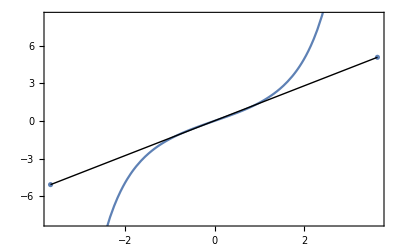

```mathematica
QuantilePlot[StudentTDistribution[0.00683314415887211,1.093621826573951,2.013323805635774]]
```

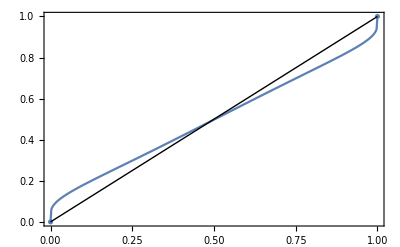

```mathematica
ProbabilityPlot[StudentTDistribution[0.00683314415887211,1.093621826573951,2.013323805635774]]
```

```mathematica
CDF[StudentTDistribution[0.00683314415887211,1.093621826573951,2.013323805635774],x]
```

Piecewise[{{1/2 BetaRegularized[2.40795/(2.40795+(-0.00683314+x)^2),1.00666,1/2], x≤0.00683314}, {1/2 (1+BetaRegularized[(-0.00683314+x)^2/(2.40795+(-0.00683314+x)^2),1/2,1.00666]), True}}]

```mathematica
PDF[StudentTDistribution[0.00683314415887211,1.093621826573951,2.013323805635774],x]
```

0.92856 (1/(2.01332+0.836114 (-0.00683314+x)^2))^1.50666

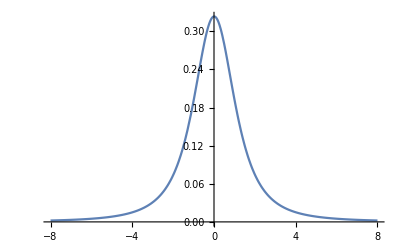

```mathematica
Plot[0.9285598188746526 (1/(2.013323805635774+0.836114319543639 (-0.00683314415887211+x)^2))^1.506661902817887,{x,-8,8}]
```

```mathematica
RandomVariate[Out@23,100]
```

{1.60548,2.74214,-1.52299,8.79262,2.06345,-0.731525,0.0122436,-2.10228,3.93998,0.100556,-0.525586,0.753523,0.0721399,-1.52728,-0.490097,-0.193388,-2.44093,-0.133416,-1.09699,1.06541,0.92209,5.18878,0.947479,0.420058,0.102197,0.768023,-1.06279,-0.226447,0.932579,1.00377,0.141606,-0.647354,-2.92753,2.25213,-1.62408,3.65879,2.73886,0.0899354,8.73612,0.259972,0.2645,2.0911,-0.0403318,0.0735786,0.283443,-0.327561,-4.18663,-0.57377,0.638473,-0.599665,0.95041,1.10789,1.23074,0.507435,1.75038,0.274475,-11.7691,-1.79951,-2.50044,0.0708033,-0.428387,-0.0285865,-2.82858,-0.693936,0.27246,1.69799,1.17573,-1.25978,-0.306296,1.05573,1.32869,0.0320321,1.15605,-0.90875,1.84016,4.78719,-0.314963,-0.0459937,-0.653475,-1.82399,0.837767,1.31765,-0.0963863,-2.18853,0.974465,-0.326849,-1.5056,-2.28918,-0.35252,-1.63876,-5.28385,0.620331,0.475797,0.451508,45.4208,0.162281,-2.46398,0.00761348,1.16884,-1.45711}

```mathematica
ContinuousWaveletTransform[%29]
```

ContinuousWaveletData[…]

```mathematica
%38["Wavelet"]
```

MexicanHatWavelet[1]

```mathematica
WaveletPsi[MexicanHatWavelet[1]]
```

-(2 ⅇ^(-#1^2/2) (-1+#1^2))/(√3 π^(1/4))&

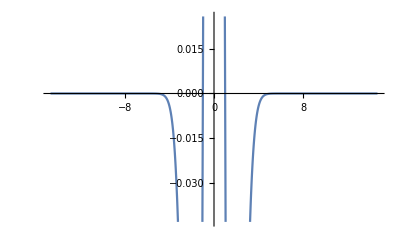

```mathematica
Plot[(-(2 ⅇ^(-#1^2/2) (-1+#1^2))/(√3 π^(1/4))&)[x],{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
WaveletPhi[MexicanHatWavelet[1]]
```

WaveletPhi[MexicanHatWavelet[1]]

```mathematica
WaveletFilterCoefficients[MexicanHatWavelet[1],"PrimalLowpass"]
```

WaveletFilterCoefficients::wfilt: Wavelet filter coefficients for MexicanHatWavelet[1] are not computable.

WaveletFilterCoefficients[MexicanHatWavelet[1],PrimalLowpass]

```mathematica
WaveletFilterCoefficients[MexicanHatWavelet[1],"PrimalHighpass"]
```

WaveletFilterCoefficients::wfilt: Wavelet filter coefficients for MexicanHatWavelet[1] are not computable.

WaveletFilterCoefficients[MexicanHatWavelet[1],PrimalHighpass]

```mathematica
InverseContinuousWaveletTransform[%38]
```

{0.0634716,1.24418,-2.33699,7.97521,1.55489,-1.76455,-1.17201,-2.70007,3.36963,-0.118772,-0.961401,0.52319,-0.165537,-1.77441,-0.650324,-0.411308,-2.52834,-0.366557,-0.949785,1.10469,1.54825,5.64299,1.48793,0.447844,0.238792,0.688666,-1.13076,-0.384297,0.956343,0.954657,0.0523128,-1.16584,-3.1545,1.76747,-1.5282,3.69834,2.86865,0.678096,9.07756,0.801913,0.270785,2.27024,0.18651,0.232007,0.611006,-0.268426,-4.02875,-0.290268,1.31842,0.226649,1.90761,2.27256,2.45585,1.76564,3.22676,0.712621,-11.2911,-1.7753,-1.35482,0.980544,0.82242,0.80946,-1.94797,0.0355471,1.31941,2.75453,2.06081,-0.597506,0.261733,1.78044,1.95857,0.663168,1.52696,-0.450265,2.51636,5.4575,0.201289,0.0360795,-0.699187,-1.85456,0.83242,1.43826,-0.397418,-2.51847,0.417607,-0.842045,-2.53773,-3.34533,-1.65619,-3.19719,-7.15194,-0.846598,-1.65641,2.26293,46.1774,1.63621,-5.19586,-1.64665,-0.844628,-3.10201}

```mathematica
%38[All]
```

{{1,1}→{0.255282+1.84003×10^-16 ⅈ,0.78356-1.79563×10^-16 ⅈ,-1.98796-2.91172×10^-16 ⅈ,2.25944+2.8229×10^-16 ⅈ,-0.6336-4.73907×10^-16 ⅈ,-0.406184+1.87462×10^-16 ⅈ,0.483097-4.25295×10^-17 ⅈ,-1.15473-3.61075×10^-16 ⅈ,85,-6.71744-8.82352×10^-16 ⅈ,12.136+8.85973×10^-16 ⅈ,-6.4145-5.78372×10^-16 ⅈ,0.282228+1.19684×10^-15 ⅈ,-0.209937-9.10702×10^-16 ⅈ,0.68192+5.42256×10^-16 ⅈ,-0.824169-1.81464×10^-16 ⅈ},18,{5,4}→{1}}
 |  |  |  |

```mathematica
WaveletScalogram[%38]
```

-Graphics-

```mathematica
Fit[%29,{1,x},x]
```

0.190109+0.00760002 x

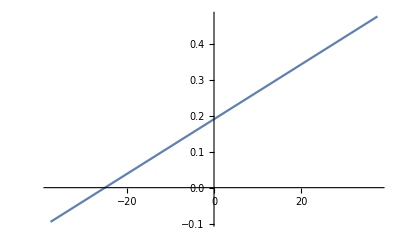

```mathematica
Plot[0.19010920475900894+0.007600018336809776 x,{x,-37.521463041392515,37.521463041392515}]
```

```mathematica
Fit[%29,{1,x,x^2},x]
```

2.02172-0.100142 x+0.00106675 x^2

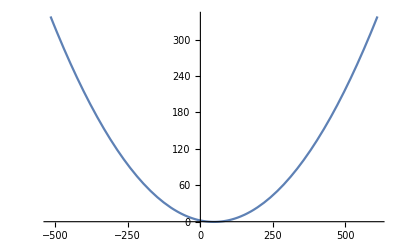

```mathematica
Plot[2.0217167019354654-0.10014159914415834 x+0.0010667486879303776 x^2,{x,-516.3154185466578,610.1909491915046}]
```

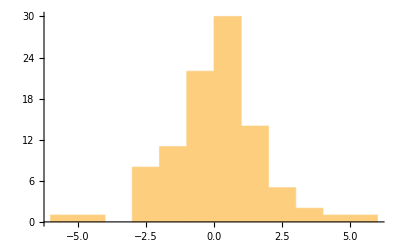

```mathematica
Histogram[%29]
```

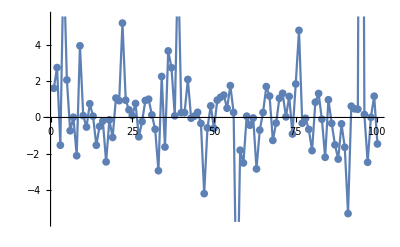

```mathematica
ListLinePlot[%29,Mesh->All]
```

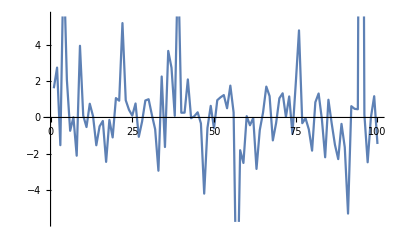

```mathematica
ListLinePlot[%29]
```

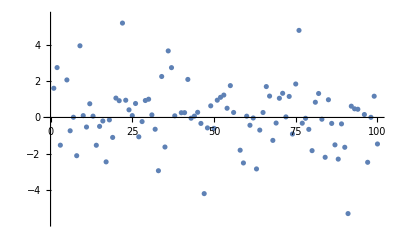

```mathematica
ListPlot[%29]
```

```mathematica
Probability[x>100,x\[Distributed]Out[23]]
```

0.0000568001

```mathematica
Table[{i,Probability[x>100,x\[Distributed]Out[23]]},{i,1,100}]
```

{{1,0.0000568001},{2,0.0000568001},{3,0.0000568001},{4,0.0000568001},{5,0.0000568001},{6,0.0000568001},{7,0.0000568001},{8,0.0000568001},{9,0.0000568001},{10,0.0000568001},{11,0.0000568001},{12,0.0000568001},{13,0.0000568001},{14,0.0000568001},{15,0.0000568001},{16,0.0000568001},{17,0.0000568001},{18,0.0000568001},{19,0.0000568001},{20,0.0000568001},{21,0.0000568001},{22,0.0000568001},{23,0.0000568001},{24,0.0000568001},{25,0.0000568001},{26,0.0000568001},{27,0.0000568001},{28,0.0000568001},{29,0.0000568001},{30,0.0000568001},{31,0.0000568001},{32,0.0000568001},{33,0.0000568001},{34,0.0000568001},{35,0.0000568001},{36,0.0000568001},{37,0.0000568001},{38,0.0000568001},{39,0.0000568001},{40,0.0000568001},{41,0.0000568001},{42,0.0000568001},{43,0.0000568001},{44,0.0000568001},{45,0.0000568001},{46,0.0000568001},{47,0.0000568001},{48,0.0000568001},{49,0.0000568001},{50,0.0000568001},{51,0.0000568001},{52,0.0000568001},{53,0.0000568001},{54,0.0000568001},{55,0.0000568001},{56,0.0000568001},{57,0.0000568001},{58,0.0000568001},{59,0.0000568001},{60,0.0000568001},{61,0.0000568001},{62,0.0000568001},{63,0.0000568001},{64,0.0000568001},{65,0.0000568001},{66,0.0000568001},{67,0.0000568001},{68,0.0000568001},{69,0.0000568001},{70,0.0000568001},{71,0.0000568001},{72,0.0000568001},{73,0.0000568001},{74,0.0000568001},{75,0.0000568001},{76,0.0000568001},{77,0.0000568001},{78,0.0000568001},{79,0.0000568001},{80,0.0000568001},{81,0.0000568001},{82,0.0000568001},{83,0.0000568001},{84,0.0000568001},{85,0.0000568001},{86,0.0000568001},{87,0.0000568001},{88,0.0000568001},{89,0.0000568001},{90,0.0000568001},{91,0.0000568001},{92,0.0000568001},{93,0.0000568001},{94,0.0000568001},{95,0.0000568001},{96,0.0000568001},{97,0.0000568001},{98,0.0000568001},{99,0.0000568001},{100,0.0000568001}}

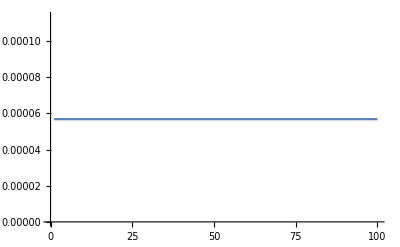

```mathematica
ListPlot[%49,Joined->True]
```

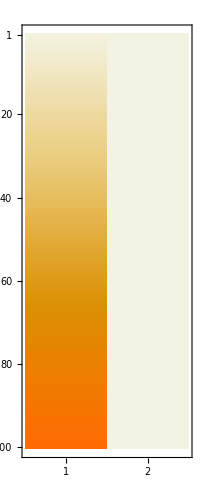

```mathematica
MatrixPlot[%49]
```

```mathematica
Table[{i,Probability[x>i,x\[Distributed]Out[23]]},{i,1,100}]
```

{{1,0.229557},{2,0.104558},{3,0.0553986},{4,0.0334144},{5,0.0221095},{6,0.0156309},{7,0.0116039},{8,0.00894103},{9,0.00709314},{10,0.00576051},{11,0.00476888},{12,0.00401161},{13,0.00342054},{14,0.00295054},{15,0.00257077},{16,0.00225959},{17,0.00200147},{18,0.00178503},{19,0.00160177},{20,0.00144527},{21,0.00131056},{22,0.00119378},{23,0.0010919},{24,0.00100249},{25,0.000923604},{26,0.000853646},{27,0.000791325},{28,0.00073557},{29,0.000685491},{30,0.000640345},{31,0.000599505},{32,0.000562441},{33,0.000528702},{34,0.000497903},{35,0.000469713},{36,0.000443845},{37,0.000420051},{38,0.000398116},{39,0.000377851},{40,0.000359092},{41,0.000341692},{42,0.000325524},{43,0.000310475},{44,0.000296443},{45,0.000283339},{46,0.000271083},{47,0.000259604},{48,0.000248837},{49,0.000238724},{50,0.000229215},{51,0.000220261},{52,0.00021182},{53,0.000203855},{54,0.00019633},{55,0.000189212},{56,0.000182474},{57,0.000176089},{58,0.000170033},{59,0.000164283},{60,0.000158819},{61,0.000153622},{62,0.000148676},{63,0.000143965},{64,0.000139473},{65,0.000135188},{66,0.000131097},{67,0.000127189},{68,0.000123452},{69,0.000119877},{70,0.000116455},{71,0.000113178},{72,0.000110036},{73,0.000107023},{74,0.000104132},{75,0.000101356},{76,0.0000986894},{77,0.0000961265},{78,0.000093662},{79,0.0000912908},{80,0.0000890083},{81,0.0000868102},{82,0.0000846923},{83,0.0000826508},{84,0.0000806821},{85,0.0000787828},{86,0.0000769496},{87,0.0000751795},{88,0.0000734697},{89,0.0000718174},{90,0.0000702201},{91,0.0000686754},{92,0.000067181},{93,0.0000657347},{94,0.0000643346},{95,0.0000629786},{96,0.0000616649},{97,0.0000603919},{98,0.0000591577},{99,0.0000579609},{100,0.0000568001}}

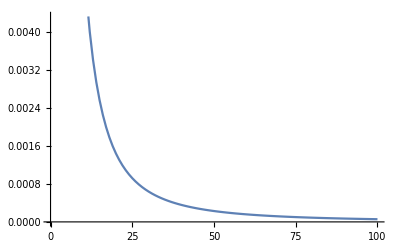

```mathematica
ListPlot[%52,Joined->True]
```

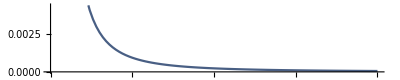

```mathematica
ListPlot[%52,
Joined->True,ColorFunction->"DarkRainbow",ImageSize->Full,AspectRatio->1/5]
```

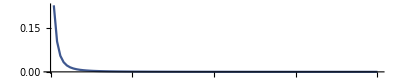

```mathematica
ListPlot[%52,
Joined->True,ColorFunction->"DarkRainbow",ImageSize->Full,AspectRatio->1/5,PlotRange->Full]
```